# DMDGP Package

```mathematica
(* Put the following two lines at the top of every notebook. *)
(* messageHandler=If[Last[#],Abort[]]&;
Internal`AddHandler["Message",messageHandler]; *)
```

## Instance Creation

### Source Code

```mathematica
SetPositionUsingCartesianSystem::usage="Set the atoms positions using atomic rotations and translations.";SetPositionUsingCartesianSystem[d_,t_,w_]:=
Module[
(* declare local variables *)
{a,b,c,v,n,R,X,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[t[[3]]],d[[3]]Sin[t[[3]]] ,0}};
(* set remaining positions *)
For[i=4,i≤numberOfAtoms,i++,
{a,b,c}={X[[i-3]],X[[i-2]],X[[i-1]]};
v= d[[i]]* Normalize[b-c]; 
(* normal to the plane abc *)
n=Cross[a-b,c-b];
(* apply plane rotation *)
R=RotationTransform[t[[i]],n];
v=R[v];
(* apply torsion rotation and translation *)
R=RotationTransform[w[[i]],c-b];
v=R[v]+c;
(* set i-th coordinate *)
X[[i]]=v
];
X
];

SetPositionUsingHomogeneousCoords::usage="Set the atoms positions using internal coordinate system.";
SetPositionUsingHomogeneousCoords[d_,t_,w_]:=
Module[
{B,B1,B2,B3,X,di,ct,st,cw,sw,v,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[t[[3]]],d[[3]]Sin[t[[3]]] ,0}};
(* set first transformation matrices *)
B1=IdentityMatrix[4];
B2={{-1,0,0,-d[[2]]},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
{ct,st}={Cos[t[[3]]],Sin[t[[3]]]};
di=d[[3]];
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
(* set remaining coordinates *)
B=B1.B2.B3;
For[i=4,i≤numberOfAtoms,i++,
{ct,st}={Cos[t[[i]]],Sin[t[[i]]]};
{cw,sw}={Cos[w[[i]]],Sin[w[[i]]]};
di=d[[i]];
(* concatenate transformation matrices *)
B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}};
(* apply transformation at origin *)
v =B.{0,0,0,1};
(* update coordinate *)
X[[i]]=v[[{1,2,3}]];
];
X
];

GenerateRandom3DBackbone::usage="Generates a random backbone in tridimensional Euclidean space.";
GenerateRandom3DBackbone[numberOfAtoms_,algorithm_:"HomogeneousCoords"]:=
Module[
(* declare the local variables *)
{d,t,w,X,output},
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
d[[1]]=0;
(* plane angles *)
t=Table[1.91,{i,numberOfAtoms}];
t[[{1,2}]]={0,0};
(* torsion angles *)
w=Table[RandomReal[2Pi],{i,numberOfAtoms}];
w[[{1,2,3}]]={0,0,0};
(* set the remaining 3d positions *)
Switch[algorithm,
"HomogeneousCoords",X=SetPositionUsingHomogeneousCoords[d,t,w],
"CartesianSystem",X=SetPositionUsingCartesianSystem[d,t,w],
_,Throw["InvalidAlgorithm"]
];
(* set output *)
<|"Points"->X,"TorsionAngles"->w,"CovalentBondLengths"->d,"PlaneRotationAngles"->t|>
];

GetMatrixDistance::usage="Gets the complete distance matrix for all coordinates in the array X.";
GetMatrixDistance[x_]:=Table[Norm[x[[i]]-x[[j]]],{i,1,Length[x]},{j,1,Length[x]}];

GenerateRandomDMDGPInstance::usage="Generates a random DMDGP instance.";
GenerateRandomDMDGPInstance[numberOfAtoms_,Dtol_:5.0]:=
Module[
(* declare local variables *)
{i,j,X,G,D,output,dij},
X=GenerateRandom3DBackbone[numberOfAtoms];
D=DistanceMatrix[X["Points"]];
G=Table[If[And[0<D[[i]][[j]],D[[i]][[j]]≤Dtol],D[[i]][[j]],Infinity],{i,1,numberOfAtoms},{j,1,numberOfAtoms}];
G=WeightedAdjacencyGraph[G];
(* set output *)
<|"X"->X,"G"->G|>
];

Plot3DBackbone::usage="Plots the points using the coordinates of X[Points].";
Plot3DBackbone[X_]:=Graphics3D[{Line[X["Points"]],{PointSize[Large],Blue,Point[X["Points"]]}}, Axes->True]

CalculateProteinAngles::usage="Calculates the protein angles (plane and torsion) considering the sequence A-B-C-D.";
CalculateProteinAngles[A_,B_,C_,D_]:=
Module[
(* Calculate the plane and torsion angles for X4 *)
{nabc, nbcd},
(* centered at C *)
Print["Angle[BCD] =",N[VectorAngle[B-C,D-C]]];
(* centered at B and C *)
{nabc,nbcd} = {Cross[A-B,C-B],Cross[B-C,D-C]};
Print["Angle[ABCD]=",N[VectorAngle[nabc,nbcd]]];
];

CalculateProteinAnglesForAtomAtPosition::usage="Calculates the protein angles (plane and torsion) to i-th atom.";
CalculateProteinAnglesForAtomAtPosition[X_,i_]:=CalculateProteinAngles[X[[i-3]],X[[i-2]],X[[i-1]],X[[i]]];
```

### Examples

#### Generating Random Backbone

```mathematica
X=GenerateRandom3DBackbone[15];
Print["X=",X];
Plot3DBackbone[X]
```

X=<|Points→{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.00375,2.34091,0.6741},{-1.66969,3.6492,1.09075},{-2.8344,3.34945,2.03005},{-4.0875,4.06125,1.52828},{-3.70473,5.05001,0.430777},{-3.50034,6.43316,1.04216},{-4.83963,7.16148,1.10954},{-5.63815,6.8743,-0.158754},{-6.39418,8.13168,-0.578391},{-6.32123,9.16556,0.541624},{-4.99216,9.02361,1.2779},{-3.84315,9.2565,0.301071}},TorsionAngles→{0,0,0,5.79567,3.46576,1.01387,4.03444,6.08639,4.6332,4.77244,5.59054,3.79665,6.09291,0.564039,1.05173},CovalentBondLengths→{0,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526},PlaneRotationAngles→{0,0,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91}|>

-Graphics3D-

#### Set Position Using Different Coordinate Systems

```mathematica
d=X["CovalentBondLengths"];
t=X["PlaneRotationAngles"];
w=X["TorsionAngles"];
S=SetPositionUsingCartesianSystem[d,t,w];
P=SetPositionUsingHomogeneousCoords[d,t,w];
Print["S=",S];
Print["P=",P];
CalculateProteinAnglesForAtomAtPosition[S,8];
CalculateProteinAnglesForAtomAtPosition[P,8];
```

S={{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.00375,2.34091,0.6741},{-1.66969,3.6492,1.09075},{-2.8344,3.34945,2.03005},{-4.0875,4.06125,1.52828},{-3.70473,5.05001,0.430777},{-3.50034,6.43316,1.04216},{-4.83963,7.16148,1.10954},{-5.63815,6.8743,-0.158754},{-6.39418,8.13168,-0.578391},{-6.32123,9.16556,0.541624},{-4.99216,9.02361,1.2779},{-3.84315,9.2565,0.301071}}

P={{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.00375,2.34091,0.6741},{-1.66969,3.6492,1.09075},{-2.8344,3.34945,2.03005},{-4.0875,4.06125,1.52828},{-3.70473,5.05001,0.430777},{-3.50034,6.43316,1.04216},{-4.83963,7.16148,1.10954},{-5.63815,6.8743,-0.158754},{-6.39418,8.13168,-0.578391},{-6.32123,9.16556,0.541624},{-4.99216,9.02361,1.2779},{-3.84315,9.2565,0.301071}}

Angle[BCD] =1.91

Angle[ABCD]=0.196794

Angle[BCD] =1.91

Angle[ABCD]=0.196794

#### Generate Random DMDGP Instance

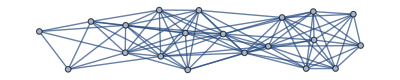
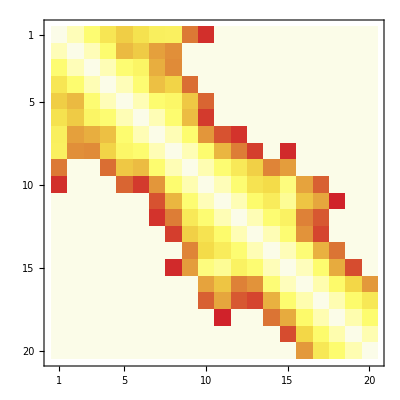
{-Graphics-,-Graphics-,-Graphics3D-}

```mathematica
M=GenerateRandomDMDGPInstance[20];
{M["G"],MatrixPlot[WeightedAdjacencyMatrix[M["G"]],ColorFunction->"TemperatureMap"],Plot3DBackbone[M["X"]]}
```

#### Timing

```mathematica
(* Comparison between HomogeneousCoords and CartesianSystem algorithms *)
(* 
Print["Time(HomogeneousCoords)=",First[Timing[Timing[GenerateRandom3DBackbone[1000,"HomogeneousCoords"]]]]];
Print["Time(CartesianSystem)=",First[Timing[Timing[GenerateRandom3DBackbone[1000,"CartesianSystem"]]]]];
*)
```

```mathematica
(* Estimating complexity of random backbone generation *)
(*
Clear[x];
tp=Table[{n,First[Timing[GenerateRandom3DBackbone[n,"HomogeneousCoords"]]]},{n,100,10000,100}];
fp=Fit[tp,{1,x},x];
Show[ListPlot[tp],Plot[{fp},{x,100,10000}],AxesLabel->{HoldForm[Problem Size],HoldForm[Time in Seconds]},PlotLabel->HoldForm[GenerateRandom3DBackbone],LabelStyle->{GrayLevel[0]}]
*)
```

## MDGP Solvers

### Source Code

```mathematica
GetEdgeWeight::usage="Gets edge weight.";
GetEdgeWeight[G_,E_]:=Module[
{i,D={}},
If[Not[FailureQ[PropertyValue[{G,E[[1]]},EdgeWeight]]],
(* E is a list of edges *)
For[i=1,i≤Length[E],i++,AppendTo[D,PropertyValue[{G,E[[i]]},EdgeWeight]]],
(* E is a single edge *)
D=PropertyValue[{G,E},EdgeWeight]
];
Return[D]
];

IsPositionValid[G_,X_,i_]:=
Module[
(* local variables *)
{j,k,V,Xi,Xj,dij,Dij,tolerance=0.001},
(* current position *)
Xi=X[[i]];
(* vertices adjacent to vertex i *)
V= AdjacencyList[G,i];
For[k=1,k≤Length[V],k++,
(* neighbor index *)
j=V[[k]]; 
(* check only the distances to the precedent atoms *)
If[j>i,Continue[]];
(* neighbor coordinate *)
Xj=X[[j]];
(* actual distance *)
dij=EuclideanDistance[Xi,Xj];
(* prescribed distance *)
Dij=GetEdgeWeight[G,i<->j];
(* check if actual distance is valid *)
If[Abs[Dij-dij]≥tolerance,Return[False]]
];
Return[True]
];

IsNaturalOrderValid[G_]:=Module[
(* local variables *)
{i,j},
For[i=4,i≤Length[VertexList[G]],i++,
For[j=1,j≤3,j++,If[FailureQ[GetEdgeWeight[G,i<->(i-j)]],Return[False]]];
];
Return[True]
];

BPGetNodePosition[G_,X_,i_,branch_]:=Module[
{j,u,v,a,b,c,delta,dy,dz,dw,ky,kz,kw,A,x3,y,z,w},
{y,z,w}=Table[X[[i-j]],{j,3}];
{dy,dz,dw}=GetEdgeWeight[G,Table[i<->(i-j),{j,3}]];
{ky,kz,kw}={dy^2-y.y,dz^2-z.z,dw^2-w.w};
(* set x[1:2]=u*x[3]+v *)
A={y[[{1,2}]]-z[[{1,2}]],y[[{1,2}]]-w[[{1,2}]]};
u=LinearSolve[A,{z[[3]]-y[[3]],w[[3]]-y[[3]]}];
v=LinearSolve[A,{(kz-ky)/2,(kw-ky)/2}];
(* set/solve the quadratic equation *)
u={u[[1]],u[[2]],1};v={v[[1]],v[[2]],0};
a=u.u;
b=2*(u.(v-y));
c=v.(v-2*y)-ky;
(* set the free coordinate *)
x3=(-b-Sqrt[b^2-4*a*c])/(2*a);
If[branch==1,x3=(-b/a)-x3];
(* set output *)
u*x3+v
];

BPSolver[G_]:=Module[
(* local variables *)
{i,j,k,tABC,dAB,dAC,dBC,done,numberOfAtoms,prune,node,branch,Xi,Xj,E,X,tree,S},
numberOfAtoms=Length[VertexList[G]];
(* check if natural order is valid *)
If[Not[IsNaturalOrderValid[G]],Throw["InvalidOrdering"]];
(* init atoms positions on Euclidean 3d space *)
X=Table[{0,0,0},{i,numberOfAtoms}];
{dAB,dAC,dBC}=GetEdgeWeight[G,{1<->2,1<->3,2<->3}];
(* planar rotation angle for atom 3 *)
tABC=ArcCos[(dAB^2+dBC^2-dAC^2)/(2*dAB*dBC)];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-dAB,0,0},{-dAB+dBC*Cos[tABC],dBC*Sin[tABC] ,0}};
(* init BPTree *)
{branch=Table[0,{i,1,numberOfAtoms}],branch[[{1,2,3}]]={1,1,1}};
{node=3,prune=False};
(* BP core *)
S={}; (* solutions *)
While[True,
(* go to next node *)
If[prune|| node==numberOfAtoms,
(* if pruned or last node, search for a node to branch *)
i=node; prune=False;
While[i>0,If[branch[[i]]==0,branch[[i]]=1;Break[]];i--];
(* there is no next node *)
If[i==0,Break[]];
(* reset lower (until k) tree levels *)
For[j=i+1,j≤node,j++,branch[[j]]=0];
node=i,
(* if not pruned nor last node, just go to the child node *)
node++
];
(* calculate position of i-th node *)
X[[node]]=BPGetNodePosition[G,X,node,branch[[node]]];
(* prune *)
If[Not[IsPositionValid[G,X,node]],prune=True;Continue[]];
(* new solution found *)
If[node==numberOfAtoms,AppendTo[S,{X,branch}]];
];
Print["A total of ", Length[S]," solutions has been found."];
Return[S]
];
```

### Examples

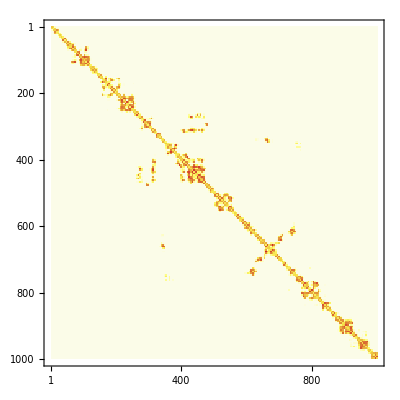

```mathematica
M=GenerateRandomDMDGPInstance[1000,5];
X=M["X"];
G=M["G"];
(* MatrixPlot[WeightedAdjacencyMatrix[G],ColorFunction->"TemperatureMap"] *)
(* MatrixPlot[WeightedAdjacencyMatrix[G],ColorFunction->"Monochrome"] *)
```

```mathematica
S=BPSolver[G];
```

A total of 2 solutions has been found.